# CS164 4.1 PCW

## Unconstrained Optimization of Differentiable Functions in Multiple Variables

Pre-Class Work

(1) Find and classify the critical points of the following functions:

Partial derivatives of the function

```mathematica
f1[x_, y_]:=-x^2+y^2
D[f1[x, y], x]
D[f1[x, y], y]
Grad[f1[x, y],{x, y}]
```

-2 x

2 y

{-2 x,2 y}

Critical point of the function (Using the partial derivative & Gradient)

```mathematica
NSolve[{D[f1[x, y], x]==0, D[f1[x, y], y]==0},{x,y}∈Reals]
NSolve[{Grad[f1[x, y],{x, y}]==0},{x,y}∈Reals]
```

{{x→0.,y→0.}}

{{x→0.,y→0.}}

```mathematica
D[f1[x, y],{{x,y},2}]
```

{{-2,0},{0,2}}

Testing to find the nature of the critical point

```mathematica
D[f1[x,y],{x,2}]
D[f1[x,y],{y,2}]
D[D[f1[x, y], x],y]
D[f1[x,y],{x,2}]*D[f1[x,y],{y,2}]-(D[D[f1[x, y], x],y])^2
```

-2

2

0

-4

The output of the test for the point (0 , 0) is -4 then it’s neither a local minimum not a local maximum but through plotting the function, we notice that the critical point represent a saddle point.

Graph of the function

```mathematica
Plot3D[f1[x,y], {x,-5,5}, {y,-5,5}]
```

-Graphics3D-

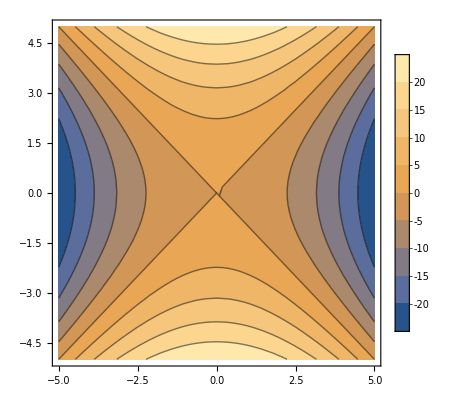

```mathematica
ContourPlot[f1[x,y],{x,-5,5}, {y,-5,5},PlotLegends->Automatic]
```

Partial derivatives of the function

```mathematica
f2[x_, y_]:=-x^6+y^3+6x-12y+7
D[f2[x, y], x]
D[f2[x, y], y]
Grad[f2[x, y],{x, y}]
```

6-6 x^5

-12+3 y^2

{6-6 x^5,-12+3 y^2}

Critical point of the function (Using the partial derivative & Gradient)

```mathematica
NSolve[{D[f2[x, y], x]==0, D[f2[x, y], y]==0},{x,y}∈Reals]
NSolve[{Grad[f2[x, y],{x, y}]==0},{x,y}∈Reals]
```

{{x→1.,y→-2.},{x→1.,y→2.}}

{{x→1.,y→-2.},{x→1.,y→2.}}

```mathematica
D[f2[x, y],{{x,y},2}]
```

{{-30 x^4,0},{0,6 y}}

Testing to find the nature of the critical point

```mathematica
D[f2[x,y],{x,2}]
D[f2[x,y],{y,2}]
D[D[f2[x, y], x],y]
D[f2[x,y],{x,2}]*D[f2[x,y],{y,2}]-(D[D[f2[x, y], x],y])^2
```

-30 x^4

6 y

0

-180 x^4 y

If we plug in the critical points found in the partial derivatives we get two options:
- For {x→1, y→-2} the output of the test is 360 and since the double derivative over x is negative then the point is a local maximum.

- For{x→1, y→2} the output of the test is -360 then it’s neither a local maximum nor a local minimum.

Graph of the function

```mathematica
Plot3D[f2[x,y], {x,-3,3}, {y,-3,3}]
```

-Graphics3D-

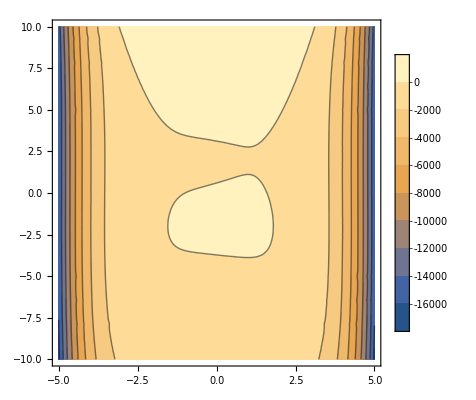

```mathematica
ContourPlot[f2[x,y],{x,-5,5}, {y,-10,10},PlotLegends->Automatic]
```

Partial derivatives of the function

```mathematica
f3[x_, y_,z_]:=(2x^2+3y^2+z^2)*Exp[-(x^2+y^2+z^2)]
D[f3[x, y,z], x]
D[f3[x, y,z], y]
D[f3[x, y,z], z]
```

4 ⅇ^(-x^2-y^2-z^2) x-2 ⅇ^(-x^2-y^2-z^2) x (2 x^2+3 y^2+z^2)

6 ⅇ^(-x^2-y^2-z^2) y-2 ⅇ^(-x^2-y^2-z^2) y (2 x^2+3 y^2+z^2)

2 ⅇ^(-x^2-y^2-z^2) z-2 ⅇ^(-x^2-y^2-z^2) z (2 x^2+3 y^2+z^2)

Critical point of the function (Using the partial derivative & Gradient)

```mathematica
NSolve[{D[f3[x, y,z], x]==0, D[f3[x, y,z], y]==0,D[f3[x, y,z], z]==0},{x,y,z}∈Reals]
NSolve[{Grad[f3[x, y,z],{x, y,z}]==0},{x,y,z}∈Reals]
```

{{x→-1.,y→0,z→0},{x→0,y→-1.,z→0},{x→0,y→0,z→-1.},{x→0,y→0,z→0},{x→0,y→0,z→1.},{x→0,y→1.,z→0},{x→1.,y→0,z→0}}

{{x→-1.,y→0,z→0},{x→0,y→-1.,z→0},{x→0,y→0,z→-1.},{x→0,y→0,z→0},{x→0,y→0,z→1.},{x→0,y→1.,z→0},{x→1.,y→0,z→0}}

```mathematica
ContourPlot3D[f3[x,y,z],{x,-2,2}, {y,-2,2},{z,-2,2},PlotLegends->Automatic]
```

-Graphics3D-

(2) A box is made of cardboard with double thick sides, a triple thick bottom, single thick front and back and no top. It’s total volume is 3 units. What box dimensions will use the least amount of cardboard? Demonstrate that the dimensions you have found actually minimize the cardboard used.

First, we write the surface of each side and multiply it by the thickness they’re supposed to have.
Then, we add the constraint that the volume has to be equal to three. In addition, the segments have to be strictly positive as having negative values is plausible.
Last, we feed these input to the NMinimize function that strive for the best values that satisfy the conditions listed above. We notice that dimensions of 2x1 and a height of 1.5 is the optimal way to reach a volume of 3 with consuming only 18 units of cardboard.

```mathematica
NMinimize[{3(x*y)+4(y*z)+2(x*z),x*y*z==3,x>0,y>0,z>0},{x,y,z}]
```

{18.,{x→2.,y→1.,z→1.5}}

(3) Given a set of N data points of the form (x_i, y_i), where i = 1, 2, . . . , N, use multivariable calculus to find the values of a ∈ R and b ∈ R such that the following fit error is minimized:

```mathematica
err=Sum[(a*Subscript[x,i]+b-Subscript[y,i])^2,{i,1,N}]
D[err,a]
D[err,b]
```

∑_(i=1)^N (b+a x_i-y_i)^2

∑_(i=1)^N (2 b x_i+2 a x_i^2-2 x_i y_i)

∑_(i=1)^N (2 b+2 a x_i-2 y_i)

err(a, b) = Sum[(a*x_i + b - y_i)^2, {i, 1, N}]

The derivative with respect to a:
Sum[2*b*x_i + 2*a*(x_i)^2 - 2*x_i* y_i]

The derivative with respect to b:
Sum[2*b + 2*a*x_i - 2*y_i]
2*N*b - 2*N*y_hat + 2*N*a*x_hat

We need to set both equations to be equal to zero so that we can find a critical point:
We start by writing b in function of a

```mathematica
b=(Sum[Subscript[y,i],{i,1,N}]-a*Sum[Subscript[x,i],{i,1,N}])/N
```

(-a ∑_(i=1)^N x_i+∑_(i=1)^N y_i)/N

Which is equivalent to the fact that b is the difference between the mean of all y and a multiplied by the mean of all x.

```mathematica
axy=Sum[(Subscript[x,i]-(Subscript[x,i])/N)(Subscript[y,i]-(Subscript[y,i])/N),{i,1,N}]
```

∑_(i=1)^N (x_i-x_i/N) (y_i-y_i/N)

```mathematica
axx=Sum[(Subscript[x,i]-(Subscript[x,i])/N)^2,{i,1,N}]
```

∑_(i=1)^N (x_i-x_i/N)^2

```mathematica
a=axy/axx
```

(∑_(i=1)^N (x_i-x_i/N) (y_i-y_i/N))/(∑_(i=1)^N (x_i-x_i/N)^2)